### Standard Definitions

```mathematica
ϕ[x_]:=If[Abs[x]>1,0,1-Abs[x]]
ϕ[l_,i_]:=If[l==-1,1,If[l==0,#,ϕ[2^l(#-2^-l(2i-1))]]]&
ϕ[lx_,ly_,i_,j_]:=ϕ[lx,i][#1]ϕ[ly,j][#2]&
ψ[lx_,ly_,i_,j_]:=ϕ[2^lx(#1-2^-lx i)]ϕ[2^ly(#2-2^-ly j)]&
ceil[x_,l_]:=If[x≥1,2^(l-1),1+Floor[2^(l-1)x]]
switch[x_]:=If[x≥1,x,1]
switch2[x_]:=If[x==-1,0,If[x==0,1,2^-x]]

column2[diag_,row_]:=If[diag<1,diag, If[row<1,diag,diag-row+1]]
column1[diag_,row_]:=If[diag==row,-1,column2[diag,row]]

getrow[perp_,diag_]:=Which[diag==-1,-1,diag==0,Min[perp,0],perp≤diag,perp,True,diag]
getcol[perp_,diag_]:=Which[diag==-1,-1,diag==0,Min[diag-perp,0],perp>0,diag-perp+1,True,diag]

endperp[n_]:=Which[n==-1,-1,n==0,1,True,n+2]

dϕ[x_]:=If[Abs[x]>1,0,
			If[x==1 ,-1/2,
			If[x==-1,1/2,
			If[x==0,0,
			If[x>0,-1,1]]]]](* Don't think I need this*)
```

```mathematica
test2D[x_,y_]:=Cos[x+y]
```

### Standard Basis

```mathematica
standardCoefficients2D[f_,lx_,ly_]:=Table[f[2^-lx i,2^-ly j],{i,0,2^lx},{j,0,2^ly}]
standardReconstruct2D[coefficients_,lx_,ly_]:=Sum[coefficients[[i+1,j+1]] ψ[lx,ly,i,j][#1,#2],{i,0,2^lx},{j,0,2^ly}]&

standardProject2D[f_,lx_,ly_]:=standardReconstruct2D[standardCoefficients2D[f,lx,ly],lx,ly]
```

### Full Basis

```mathematica
getCoefficient[f_,x_,l_]:=N@If[l==-1,f[0],If[l==0,f[1]-f[0],f[x]-1/2 f[x+2^-l]-1/2 f[x-2^-l]]]

getCoefficient2D[f_,x_,y_,lx_,ly_]:=getCoefficient[Function[y1,getCoefficient[Function[x1,f[x1,y1]],x,lx]],y,ly]
(* Tensor product construction
*)

fullCoefficients2D[f_,lx_,ly_]:=Table[Table[getCoefficient2D[f,2^-kx i,2^-ky j,kx,ky],{i,1,2^switch[kx]-1,2},{j,1,2^switch[ky]-1,2}],{kx,-1,lx},{ky,-1,ly}]


Reconstruct2D[coefficients_]:= Sum[coefficients[[kx+2,ky+2,ceil[#1,switch[kx]],ceil[#2,switch[ky]]]] 
ϕ[kx,ky,ceil[#1,switch[kx]],ceil[#2,switch[ky]]][#1,#2]
,{kx,-1,Length[coefficients]-2},{ky,-1,Length[coefficients]-2}]&

reverseFlatten[coefficients_,kx_,ky_]:=Module[{k},k=0;Return[Table[Table[coefficients[[++k]] ,{i,1,2^(switch[lx]-1)},{j,1,2^(switch[ly]-1)}],{lx,-1,kx},{ly,-1,ky}]];]


project2D[f_,lx_,ly_]:=Reconstruct2D[fullCoefficients2D[f,lx,ly]]
```

### Sparse Basis

```mathematica
sparseCoefficients2D[f_,n_]:=Table[Table[Table[getCoefficient2D[f,switch2[getrow[perp,diag]] i,switch2[getcol[perp,diag]] j,getrow[perp,diag],getcol[perp,diag]],{i,1,2^switch[getrow[perp,diag]]-1,2},{j,1,2^switch[getcol[perp,diag]]-1,2}],{perp,-1,endperp[diag]}],{diag,-1,n}]

sparseReconstruct[coefficients_]:=Sum[Sum[coefficients[[diag+2,perp+2,ceil[#1,switch[getrow[perp,diag]]],ceil[#2,switch[getcol[perp,diag]]]]] 
ϕ[getrow[perp,diag],getcol[perp,diag],ceil[#1,switch[getrow[perp,diag]]],ceil[#2,switch[getcol[perp,diag]]]][#1,#2]
,{perp,-1,endperp[diag]}],{diag,-1,Length[coefficients]-2}]&

sparseProject[f_,n_]:=sparseReconstruct[sparseCoefficients2D[f,n]]

sparseIntegrate[f_,n_]:=Sum[Sum[Sum[f[switch2[getrow[perp,diag]]i,switch2[getcol[perp,diag]]j],{i,1,2^switch[getrow[perp,diag]]-1,2},{j,1,2^switch[getcol[perp,diag]]-1,2}],{perp,-1,endperp[diag]}],{diag,-1,n}]
```

### Differentiation

```mathematica
diffx[f_,l_]:=
If[#1< 2^-l,(f[#1+2^(-l-1),#2]-f[#1,#2])/2^-l,If[#1> 1-2^-l,(f[#1,#2]-f[#1-2^(-l-1),#2])/2^-l,(f[#1+2^-l,#2]-f[#1-2^-l,#2])/(2 2^-l) ]]&(*If[#1< 2^-l, diffx[diffx[f,l+1],l+1][2^-l,#2]#1,If[#1> 1-2^-l, diffx[diffx[f,l+1],l+1][1-2^-l,#2](#1-1),(f[#1+2^-l,#2]-f[#1-2^-l,#2])/(2 2^-l) ]]&*)

diffy[f_,l_]:=
If[#1< 2^-l,(f[#1+2^(-l-1),#2]-f[#1,#2])/2^-l,If[#1> 1-2^-l,(f[#1,#2]-f[#1-2^(-l-1),#2])/2^-l,(f[#1+2^-l,#2]-f[#1-2^-l,#2])/(2 2^-l) ]]&(*If[#2< 2^-l, diffy[diffy[f,l+1],l+1][#1,2^-l]#2,If[#2> 1-2^-l, diffy[diffy[f,l+1],l+1][#1,1-2^-l](#2-1),(f[#1,#2+2^-l]-f[#1,#2-2^-l])/(2 2^-l)]]&*)
```

### Algorithms to form the D Matrices

```mathematica
dxMatrix[lx_,ly_]:=Flatten[Table[Table[fullCoefficients2D[diffx[ϕ[kx,ky,i,j],lx],lx,ly]//Flatten,{i,1,2^(switch[kx]-1)},{j,1,2^(switch[ky]-1)}],{kx,-1,lx},{ky,-1,ly}],3]
dyMatrix[lx_,ly_]:=Flatten[Table[Table[fullCoefficients2D[diffy[ϕ[kx,ky,i,j],lx],lx,ly]//Flatten,{i,1,2^(switch[kx]-1)},{j,1,2^(switch[ky]-1)}],{kx,-1,lx},{ky,-1,ly}],3]


dxMatrixStandard[lx_,ly_]:=Flatten[Table[standardCoefficients2D[diffx[ψ[lx,ly,i,j],lx],lx,ly]//Flatten,{i,0,2^lx},{j,0,2^ly}],1]
dyMatrixStandard[lx_,ly_]:=Flatten[Table[standardCoefficients2D[diffy[ψ[lx,ly,i,j],lx],lx,ly]//Flatten,{i,0,2^lx},{j,0,2^ly}],1]


dxMatrixSparse[n_]:=Flatten[Table[Table[Table[sparseCoefficients2D[diffx[ϕ[row,diag-row-1,i,j],n],n]//Flatten,{i,1,2^(switch[row]-1)},{j,1,2^(switch[diag-row-1]-1)}],{row,-1,diag}],{diag,-1,n}],3]

dyMatrixSparse[n_]:=Flatten[Table[Table[Table[sparseCoefficients2D[diffy[ϕ[row,diag-row-1,i,j],n],n]//Flatten,{i,1,2^(switch[row]-1)},{j,1,2^(switch[diag-row-1]-1)}],{row,-1,diag}],{diag,-1,n}],3]
```

```mathematica
sparseSection[n_,kx_,ky_]:=If[(kx>0 &&ky>0), If[kx+ky>n,0,1],If[kx>n || ky>n,0,1]]

sparseEmbedding[n_]:=Flatten[Table[Table[sparseSection[n,kx,ky],{i,1,2^(switch[kx]-1)},{j,1,2^(switch[ky]-1)}],{kx,-1,n},{ky,-1,n}],3]
```

```mathematica
Table[#[[i,i]],{i,1,81}]&@sparseEmbedding[3]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

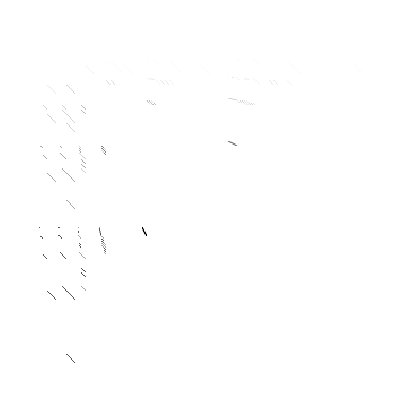

```mathematica
#1.#2-#2.#1&[dxMatrix[4,4],sparseEmbedding[4]]//ArrayPlot
```

```mathematica
Table[Sqrt[(2^-6)^2 Sum[(test2D[x,y]-#[x,y])^2,{x,0.01,1,2^-6},{y,0.01,1,2^-6}]&@sparseProject[test2D,n]]//N,{n,1,8}]
```

{0.0251743,0.00657039,0.00169819,0.000440414,0.00011763,0.0000368255,8.50077×10^-6,2.59018×10^-6}

```mathematica
sparseError2={0.027014112462531867,0.00757616246655969,0.0020888184112343427,0.0005706304725197153,0.00015477287387275615,0.000036825486582472205,8.500770260862527*^-6,2.5901831665621765*^-6}
```

{0.0251743,0.00657039,0.00169819,0.000440414,0.00011763,0.0000368255,8.50077×10^-6,2.59018×10^-6}

```mathematica
Table[Sqrt[(.005)^2 Sum[(test2D[x,y]-#[x,y])^2,{x,0,1,.005},{y,0,1,.005}]&@sparseProject[test2D,n]]//N,{n,1,5}]
```

```mathematica
sparseError2={0.027014112462531867,0.00757616246655969,0.0020888184112343427,0.0005706304725197153,0.00015477287387275615,0.00004175531062197106,0.000011212337863803431,2.9933461908806863*^-6,7.962955961280505*^-7,2.1102049143402773*^-7,5.5790440149218446*^-8,1.4676457332174641*^-8}
```

{0.0270141,0.00757616,0.00208882,0.00057063,0.000154773,0.0000417553,0.0000112123,2.99335×10^-6,7.96296×10^-7,2.1102×10^-7,5.57904×10^-8,1.46765×10^-8}

```mathematica
Sqrt[(.005)^2 Sum[(test2D[x,y]-#[x,y])^2,{x,0,1,.005},{y,0,1,.005}]&@sparseProject[test2D,12]]//N
```

1.46765×10^-8

```mathematica
Sqrt[(.01)^2 Sum[(test2D[x,y]-#[x,y])^2,{x,0,1,.01},{y,0,1,.01}]&@project2D[test2D,7,7]]//N
```

6.35067×10^-6

```mathematica
fullError={0.02524008289780807,0.00644999,0.0016204219737433931,0.0004062798404350583,0.0001015966883936506,0.000025402687440491205,6.350669922665702*^-6}
```

{0.0252401,0.00644999,0.00162042,0.00040628,0.000101597,0.0000254027,6.35067×10^-6,7.96296×10^-7}

```mathematica
Sqrt[(2^-6)^2 Sum[(test2D[x,y]-#[x,y])^2,{x,0.01,1,2^-6},{y,0.01,1,2^-6}]&@sparseProject[test2D,4]]//N
```

0.000428877

```mathematica
test2D[x_,y_]:=Cos[x+y]
```

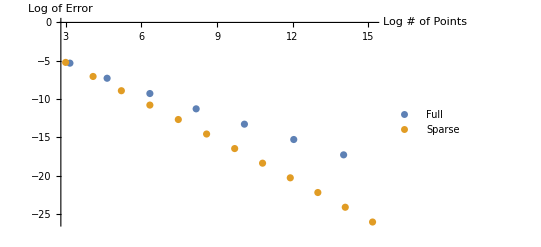

```mathematica
ListPlot[{Table[{fullLengths[[n]],fullError[[n]]//Log2},{n,1,7}],
Table[{sparseLengths[[n]],sparseError2[[n]]//Log2},{n,1,12}]}
,PlotRange->All,AxesLabel->{"Log # of Points", "Log of Error"},PlotLegends->{"Full","Sparse"}]
```

```mathematica
Table[{Length[Flatten[sparseCoefficients2D[test2D,n]]]//Log2,sparseError2[[n]]//Log2},{n,7,9}]
```

{{Log[833]/Log[2],-16.4446},{Log[1793]/Log[2],-18.3498},{Log[3841]/Log[2],-20.2602}}

```mathematica
Table[{Length[Flatten[fullCoefficients2D[test2D,n,n]]]//Log2,fullError[[n]]//Log2},{n,5,7}]
```

{{Log[1089]/Log[2],-13.2649},{Log[4225]/Log[2],-15.2647},{Log[16641]/Log[2],-17.2647}}

```mathematica
fullLengths=Table[Length[Flatten[fullCoefficients2D[test2D,n,n]]] //Log2,{n,1,7}]
```

{Log[9]/Log[2],Log[25]/Log[2],Log[81]/Log[2],Log[289]/Log[2],Log[1089]/Log[2],Log[4225]/Log[2],Log[16641]/Log[2]}

```mathematica
sparseLengths=Table[Length[Flatten[sparseCoefficients2D[test2D,n]]] //Log2,{n,1,12}]
```

{3,Log[17]/Log[2],Log[37]/Log[2],Log[81]/Log[2],Log[177]/Log[2],Log[385]/Log[2],Log[833]/Log[2],Log[1793]/Log[2],Log[3841]/Log[2],Log[8193]/Log[2],Log[17409]/Log[2],Log[36865]/Log[2]}

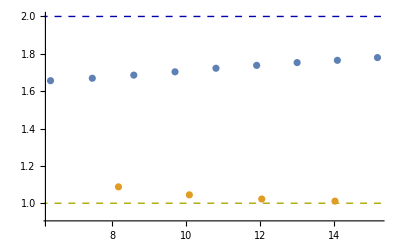

```mathematica
Show[ListPlot[{Table[{sparseLengths[[n]],-(Log2[sparseError2[[n]]]-Log2[sparseError2[[n-1]]])/(sparseLengths[[n]]-sparseLengths[[n-1]]) }//N,{n,4,12}],Table[{fullLengths[[n]],-(Log2[fullError[[n]]]-Log2[fullError[[n-1]]])/(fullLengths[[n]]-fullLengths[[n-1]]) }//N,{n,4,7}]},PlotRange->{.9,2}],Graphics[{Dashed,Darker[Yellow],Line[{{0,1},{20,1}}],Darker[Blue],Line[{{0,2},{20,2}}]}]]
```

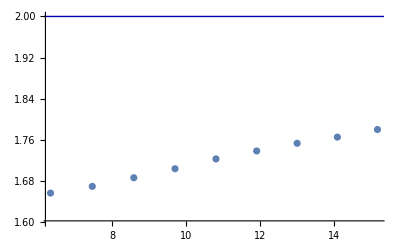

```mathematica
Show[ListPlot[{Table[{sparseLengths[[n]],-(Log2[sparseError2[[n]]]-Log2[sparseError2[[n-1]]])/(sparseLengths[[n]]-sparseLengths[[n-1]]) }//N,{n,4,12}]},PlotRange->{1.6,2}],Graphics[{Darker[Blue],Line[{{0,2},{20,2}}]}]]
```

This plot makes it seem uncertain whether the sparse error is tending to a slope of -2. It’s more clear once we approximate the length O(n + log n) as O(n), and note that then the differences in lengths are 1 instead of 1 + log(n/(n-1). The trend clearer here:

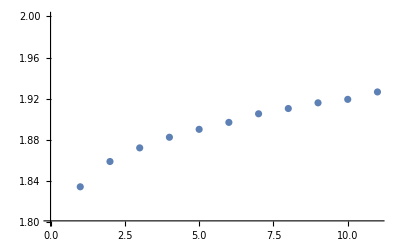

```mathematica
ListPlot[Table[-(Log2[sparseError2[[n]]]-Log2[sparseError2[[n-1]]]),{n,2,12}],PlotRange->{1.8,2}]
```